# Motorbike net2 & net3

## Set Environment

```mathematica
home = "Y:/vault/pascal/";workdir = "C:/users/lichao/git/geonb/";
```

```mathematica
SetDirectory[workdir];Needs["Posecpp`","posecpp_network.wl"];
```

```mathematica
prefix = "";suffix="";
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{316845,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

321

590

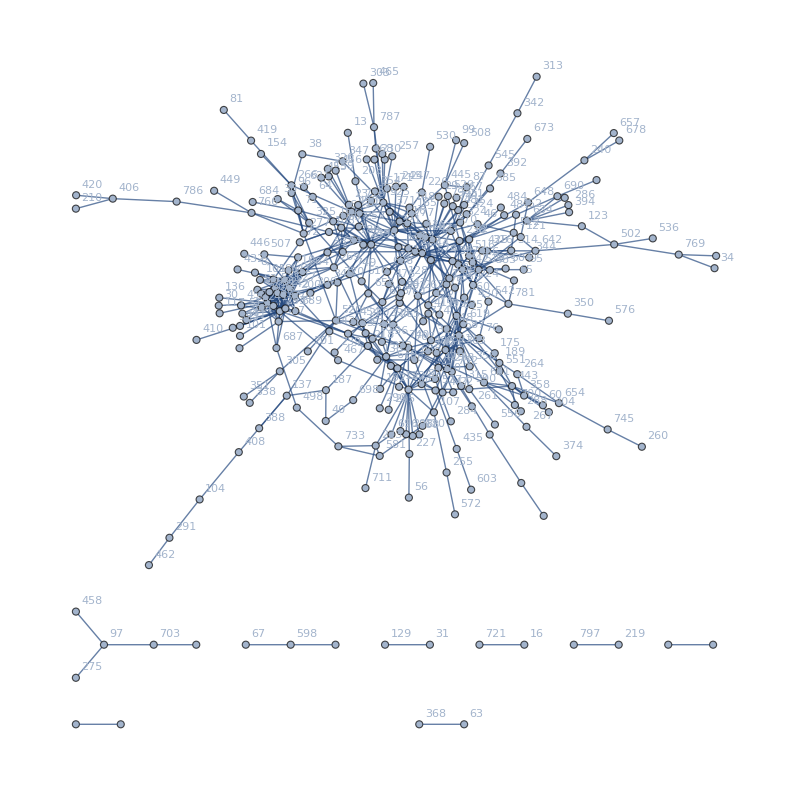

```mathematica
g2
```

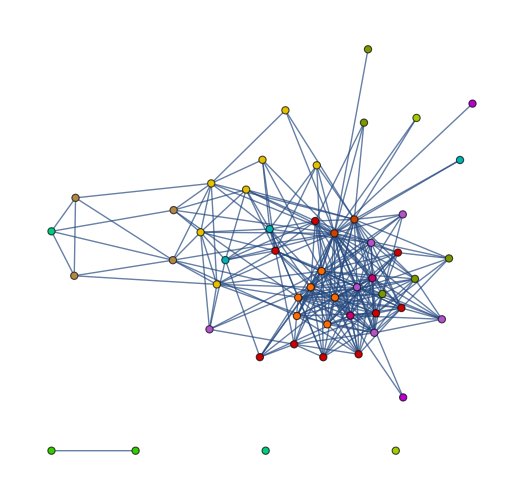

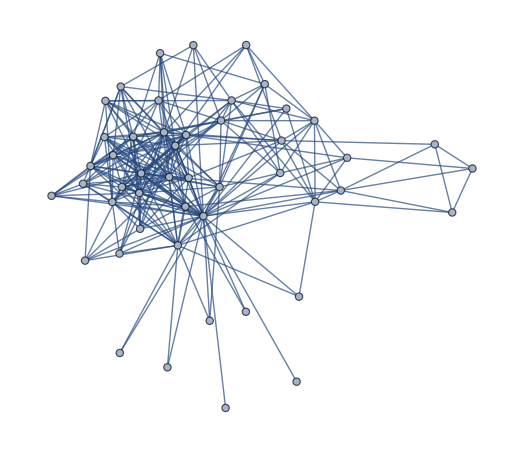

```mathematica
interGraph = Subgraph[g2,VertexList[g3]];
HighlightGraph[interGraph,comp3]
newg2= Subgraph[g2,ConnectedComponents[interGraph][[1]]]
```

```mathematica
VertexCount[newg2]
EdgeCount[newg2]
```

48

262

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

Y:/vault/pascal/net2_el.txt

## Load Network 2

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_02_02"<>suffix<>".txt"]
```

{36<->277,53<->92,54<->789,142<->477,200<->233,200<->780,233<->606,327<->566,340<->464,356<->707,358<->443,358<->700,359<->752,429<->587,429<->681,443<->587,443<->681,443<->707,447<->451,606<->641,631<->674,664<->674}

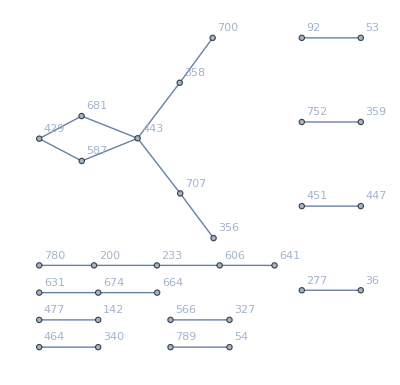

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
EdgeList[g3]//Length
```

88

71

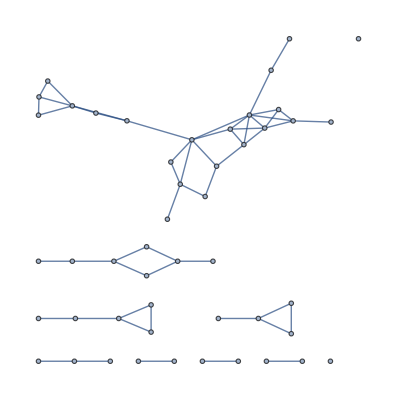

```mathematica
newg3=Subgraph[g3,newg2]
```

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{895,982,151,245,670,710,786,751,861,60,422,208,744,847,777,585,314,689,313,690,104,512,523,354,541,746,1004,517,637,771,783,787,798,844,693,954,841,451,496,785,902,130,418,615,811,968,890,709,362,100,804,969,538,923,338,248,503,561,613,162,227,207,913,921,794,887,724,178},{262,513,685,822,190,707,152,560,987,107,433,827,896,748,573,914,997,446,762},{29,10,137,263,228,348,453,653,93,352,520,35},{688,204,702,935,302,978,946,435,649,504,735,986},{320,117,458,128,624,629,635,98,74,264},{465,764,553,65,568,399,869,45,886},{889,3,161,965,938,960,518},{673,192,163,683},{57,223,554,53},{146,609,601},{604,643,888},{149,23,607},{225,25,555},{510,570,944},{701,605},{7,487},{368,188},{284,488},{115,389},{680,625},{46,145},{602,578},{577,729},{175,475},{580,200}}

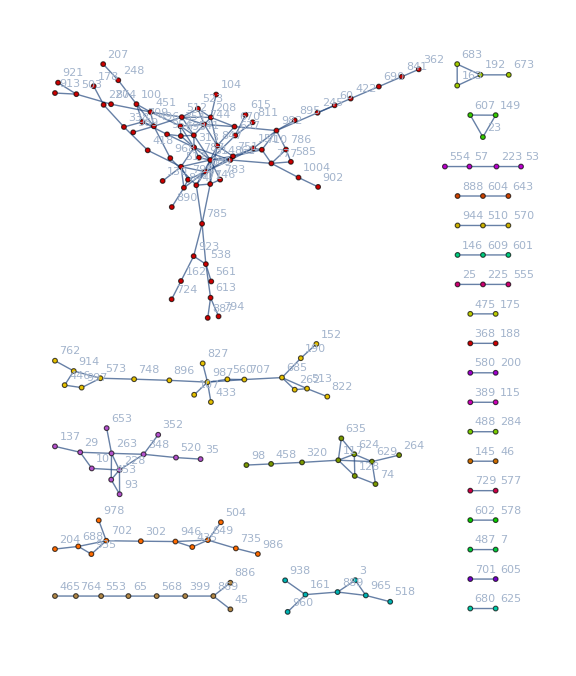

```mathematica
HighlightGraph[g3,comp3,ImageSize->Large]
```

```mathematica
Export[home<>prefix<>"net3_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/net3_plot_64.pdf

```mathematica
comp3=FindGraphCommunities[Graph[el3]]
```

{{151,861,104,208,613,746,884,118,162,785,923,637,670,751,847,314,512,523,541,744,313,354,787,947,689,771,783,798,489,538,887},{28,60,189,245,585,710,777,786,1004,422,446,914,982,997,690,688,935,702,895},{100,248,451,496,709,130,517,227,338,693,418,954,968,969,844,804,890},{223,387,605,726,261,404,735,302,946,649,919,435,701,543,839,828},{23,149,553,607,45,65,568,817,283,484,615,811},{161,294,888,938,960,291,465,764,869,583,604,886},{55,653,93,453,228,263,348,999,276,352,996},{3,889,965,225,555,518,741},{74,629,117,320,624,635,264},{91,235,316,284,488,815},{102,271,810,910,408},{556,696,872,1003},{200,580,822},{299,594,800},{439,625,680},{1,816},{39,51},{57,554},{68,961},{133,762},{147,643},{190,793},{192,673},{326,389},{362,841},{510,944},{557,559},{578,602},{601,609},{707,987},{806,922},{901,918}}

```mathematica
comp3=FindGraphCommunities[newg3]
```

{{105,268,626,736,612,501,304,744,763},{43,106,107,193,477,671,717},{79,311,72,95,239,485},{139,294,298,368,487,536},{382,546,742,630,591},{792,576,507,100},{160,187,140},{328,480},{555,728},{35,260},{16},{434}}